```mathematica
ClearAll["Global`*"]
```

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
χ=x[[15]];
Growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
Starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
InvaderStarvation =  N[ts*-Bm/(Em*(Log[1-f0*M^(γ-1)] + Log[M/(M*(1+χ))]))]*(1+RandomReal[{-noise,noise}]);
Mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
Recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
InvaderRecovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(1+χ)*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
Maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
InvaderMaintenance = (ts*ef*B0*(M*(1+χ))^η)*(1+RandomReal[{-noise,noise}]);
Resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{Growth,Starvation,Mortality,Recovery,Maintenance,Resourcegrowth,InvaderStarvation,InvaderRecovery,InvaderMaintenance}
);
```

```mathematica
FEq =λ*F-σ*(1-R)*F +ρ* R * H;
HEq =σ*(1-R)*F - ρ* R*H - μ*H;

FIEq =λ*FI-σ2*(1-R)*FI +ρ2* R * HI;
HIEq =σ2*(1-R)*FI- ρ2* R*HI - μ*HI;

REq=α*R*(1-R) -(ρ*H + β*F +ρ2*HI + β2*FI )*R ;
```

```mathematica
Solutions=FullSimplify[Solve[{FEq==0,HEq==0,FIEq==0,HIEq==0,REq==0},{F,H,FI,HI,R}]]
Length[Solutions]
```

{{F→0,H→0,FI→0,HI→0,R→0},{F→0,H→0,FI→0,HI→0,R→1},{F→(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),H→(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),FI→0,HI→0,R→(μ (-λ+σ))/(λ ρ+μ σ)},{F→0,H→0,FI→(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),HI→(α λ^2 (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),R→(μ (-λ+σ2))/(λ ρ2+μ σ2)}}

4

```mathematica
Manipulate[
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^i,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.00001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];
SpSolAll=Solutions/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderMaintenance};
SpSol=SpSolAll[[3;;4]];
Show[{
LogPlot[{None,H/.SpSol,F/.SpSol},{chi,-1,1},PlotRange->All,Frame->True,AxesOrigin->{0,0},ImageSize->400],
LogPlot[{None,HI/.SpSol,FI/.SpSol},{chi,-1,1},PlotRange->{0,All},PlotStyle->Dashed]
}],
{i,0,8,0.001}]
```

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::take: Cannot take positions 3 through 4 in Solutions.

ReplaceAll::reps: {Solutions ⟦ 3 ;; 4 ⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

Part::partw: Part 7 of {0., 0., 0.  + 0.\ ⅈ, 0., 0., 0.} does not exist.

Part::partw: Part 8 of {0., 0., 0.  + 0.\ ⅈ, 0., 0., 0.} does not exist.

Part::partw: Part 9 of {0., 0., 0.  + 0.\ ⅈ, 0., 0., 0.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity\ ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0,(5.69295×10^-15 (1.0813×10^-6+(5.72698×10^-7)/((-4.28163-3.14159 ⅈ)+Log[1.-87.0788 (1.+chi)^(1/4)])))/((6.32701×10^-8 (1+chi)^(3/4)+(6.03042×10^-15)/((-4.28163-3.14159 ⅈ)+Log[1.-87.0788 (1.+chi)^(1/4)])) (-(2.47702×10^-12)/(-0.685836+Log[1./(1.+chi)])+(6.03042×10^-15)/((-4.28163-3.14159 ⅈ)+Log[1.-87.0788 (1.+chi)^(1/4)])))}

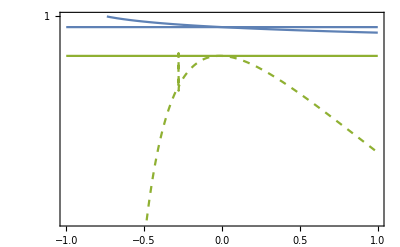

```mathematica
FI/.SpSol
```

```mathematica
chi/.FindMaximum[InvaderStarvation,{chi,-0.3}][[2]]
```

FindMaximum::nrnum: The function value -3.57061×10^-7 - 4.38305×10^-7\ ⅈ is not a real number at {chi} = {-13.3}.

-0.3

```mathematica
InvaderStarvation
```

-(2.29079×10^-6)/(-0.253671+Log[1./(1.+chi)])

```mathematica
Rationalize[Denominator[InvaderStarvation]-Log[1/(1.+chi)]]
```

-0.253671

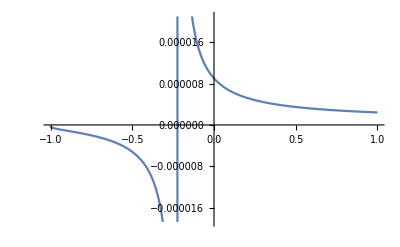

```mathematica
Plot[InvaderStarvation,{chi,-1,1}]
```

```mathematica
FISol=FI/.SpSol[[2]]
FindMaximum[FISol,chi]
```

(3.06323×10^-13 (4.6696×10^-6+(5.72698×10^-7)/((-1.10769-3.14159 ⅈ)+Log[1.-4.07767 (1.+chi)^(1/4)])))/((2.80565×10^-11 (1+chi)^(3/4)+(7.51374×10^-14)/((-1.10769-3.14159 ⅈ)+Log[1.-4.07767 (1.+chi)^(1/4)])) (-(1.06971×10^-11)/(-0.0496698+Log[1/(1.+chi)])+(7.51374×10^-14)/((-1.10769-3.14159 ⅈ)+Log[1.-4.07767 (1.+chi)^(1/4)])))

{3149.11,{chi→1.53508}}

```mathematica
Re[chi/.FindRoot[FISol,{chi,1}]]
```

-0.338142

```mathematica
ChiValues =Table[i,{i,-0.5,1,0.0001}];
Data=Table[Re[DFISol/.chi->Chi],{Chi,ChiValues}];
P=FindPeaks[Data]
```

{{1,19667.4},{4437,2.54726×10^10}}

```mathematica
P[[2]][[1]]
```

4437

```mathematica
ChiValues[[P[[2]][[1]]]]
```

-0.0564

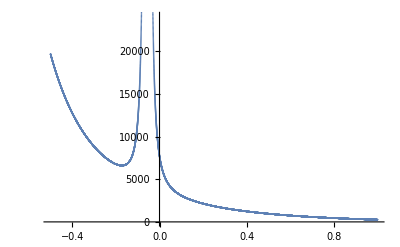

```mathematica
ListPlot[Transpose[{ChiValues,Data}]]
```

```mathematica
DFISol=D[FISol,chi];
```

```mathematica
Re[chi/.FindRoot[DFISol,{chi,-0.5}]]
```

1.53508

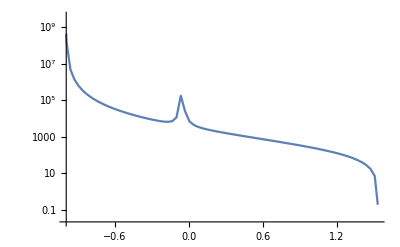

```mathematica
LogPlot[DFISol,{chi,-100,2},PlotRange->All]
```

```mathematica
FindRoot[Log[DFISol],{chi,-0.8}]
```

{chi→-120.106-242.43 ⅈ}

```mathematica
FindRoot[DFISol,chi]
```

FindRoot::fdss: Search specification chi should be a list with 1 to 5 elements.

FindRoot[DFISol,chi]

```mathematica
FSol=(F/.SpSol[[1]])
FISol=(FI/.SpSol[[2]])
```

2707.79

(1.36762×10^-12 (5.65671×10^-6+(5.72698×10^-7)/(1.79756+Log[1.-0.837361 (1.+chi)^(1/4)])))/((2.94318×10^-13 (1+chi)^(3/4)+(2.76921×10^-13)/(1.79756+Log[1.-0.837361 (1.+chi)^(1/4)])) (-(1.29583×10^-11)/(-0.0146565+Log[1./(1.+chi)])+(2.76921×10^-13)/(1.79756+Log[1.-0.837361 (1.+chi)^(1/4)])))

```mathematica
NSolve[Rationalize[FISol==FSol],chi,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{chi→-0.0145496},{chi→-3.80436×10^-17},{chi→0.0496532}}

```mathematica
FISol/.chi->0.04965324464100864
```

2707.79

```mathematica
FSol
```

2707.79

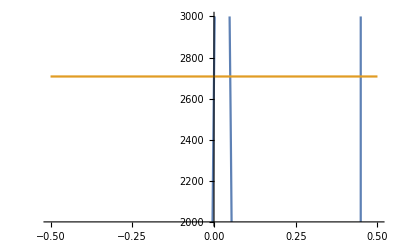

```mathematica
Plot[{Re[ FISol],FSol},{chi,-0.5,0.5},PlotRange->{2000,3000}]
```

There are 2 coexistence points...

Finding invadable chi as a function of body mass:

```mathematica
FEq =λ*F-σ*(1-R)*F +ρ* R * H;
HEq =σ*(1-R)*F - ρ* R*H - μ*H;

FIEq =λ*FI-σ2*(1-R)*FI +ρ2* R * HI;
HIEq =σ2*(1-R)*FI- ρ2* R*HI - μ*HI;

REq=α*R*(1-R) -(ρ*H + β*F +ρ2*HI + β2*FI )*R ;

Solutions=FullSimplify[Solve[{FEq==0,HEq==0,FIEq==0,HIEq==0,REq==0},{F,H,FI,HI,R}]];
```

```mathematica
MassValues = Table[10^i,{i,0,8,0.1}];
labels = Table[ToString[i],{i,0,8,0.1}];
InvasionMass=ParallelTable[
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];
SpSolAll=Solutions/.{α->Re[Resourcegrowth],λ->Re[Growth],σ->Re[Starvation],ρ->Re[Recovery],β->Re[Maintenance],μ->Re[Mortality],σ2->Re[InvaderStarvation],ρ2->Re[InvaderRecovery],β2->Re[InvaderMaintenance]};
SpSol=SpSolAll[[4]];
FSol=(H/.SpSolAll[[3]])+(F/.SpSolAll[[3]]);
MinChi =Rationalize[Denominator[InvaderStarvation]-Log[1/(1.+chi)]];
SpSolNum=Table[{i,(HI/.(SpSol/.chi->i))+(FI/.(SpSol/.chi->i))},{i,MinChi,1,0.0001}];
SpSolPositive=Select[SpSolNum,#[[2]]>FSol&];
{Mass,SpSolPositive,MinChi},
{Mass,MassValues}];
```

$Aborted

```mathematica
IMValues=Table[InvasionMass[[i]][[2]][[All,1]],{i,1,Length[InvasionMass]}];
MinChiValues=Table[InvasionMass[[i]][[3]],{i,1,Length[InvasionMass]}];
MinInvadeValues = Table[RankedMin[InvasionMass[[i]][[2]][[All,1]],50],{i,1,Length[InvasionMass]}];
MaxInvadeValues =  Table[Max[InvasionMass[[i]][[2]][[All,1]]],{i,1,Length[InvasionMass]}];
```

```mathematica
InvasionPlot=
Show[{
DistributionChart[IMValues, Method->{"BoxWidth"->"Fixed"},ChartElementFunction->ChartElementData["LineDensity",Bins->100,PointSize->0.05,"PointStyle"->ColorData[97,4]],PlotRange->{-1,1},ChartLabels->labels,ChartStyle->Directive[{Gray,Opacity[1],EdgeForm[None]}],AspectRatio->1,FrameLabel->{"Mass = 10^i","Proportion added mass χ"},ImageSize->300],
ListPlot[Transpose[{Table[i,{i,1,9}],MinChiValues}],Joined->True,PlotStyle->Transparent,Filling->Bottom],
ListPlot[Transpose[{Table[i,{i,1,9}],MinChiValues}]],
Graphics[Text["M_opt",{7,0.1}]]
}]
```

-Graphics-

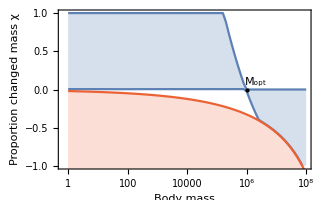

```mathematica
InvasionPlot=Show[{
ListLogLinearPlot[{Transpose[{MassValues,MinInvadeValues}],Transpose[{MassValues,MaxInvadeValues}]},Joined->True,PlotStyle->ColorData[97,1],PlotRange->{-1,1},Filling->{1->{2}},FillingStyle->Directive[ColorData[97,1],Opacity[0.25]],Frame->True,FrameLabel->{"Body mass","Proportion changed mass χ"}],
(*ListLogLinearPlot[Transpose[{MassValues,MaxInvadeValues}],Joined->True],*)
ListLogLinearPlot[Transpose[{MassValues,MinChiValues}],Joined->True,Filling->Bottom,PlotStyle->ColorData[97,4]],
Graphics[{PointSize[Large],Point[{Log@(10^6),0}]}],
Graphics[Text["M_opt",{Log@(2*10^6),0.1}]]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Invasion.pdf",InvasionPlot,"PDF",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Invasion.pdf

```mathematica
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
```

```mathematica
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];
```

```mathematica
Solutions
```

{{F→0,H→0,FI→0,HI→0,R→0},{F→0,H→0,FI→0,HI→0,R→1},{F→(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),H→(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),FI→0,HI→0,R→(μ (-λ+σ))/(λ ρ+μ σ)},{F→0,H→0,FI→(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),HI→(α λ^2 (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),R→(μ (-λ+σ2))/(λ ρ2+μ σ2)}}

```mathematica
SpSolAll=Solutions/.{α->Re[Resourcegrowth],λ->Re[Growth],σ->Re[Starvation],ρ->Re[Recovery],β->Re[Maintenance],μ->Re[Mortality],σ2->Re[InvaderStarvation],ρ2->Re[InvaderRecovery],β2->Re[InvaderMaintenance]};
```

```mathematica
FPSolutions = {(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2))}/.{α->Re[Resourcegrowth],λ->Re[Growth],σ->Re[Starvation],ρ->Re[Recovery],β->Re[Maintenance],μ->Re[Mortality],σ2->Re[InvaderStarvation],ρ2->Re[InvaderRecovery],β2->Re[InvaderMaintenance]};
```

```mathematica
Simplify[Recovery/InvaderRecovery]
```

(-40.6343-34.6625 ⅈ)+11.0334 Log[1.-44.531 (1.+chi)^(1/4)]

```mathematica
Plot[{
```

```mathematica
Show[{
Plot3D[FPSolutions[[1]],{chi,-1,1},{Mass,0,10^7},PlotStyle->ColorData[97,1]],
Plot3D[FPSolutions[[2]],{chi,-1,1},{Mass,0,10^7},PlotStyle->ColorData[97,2]]
}]
```

-Graphics3D-

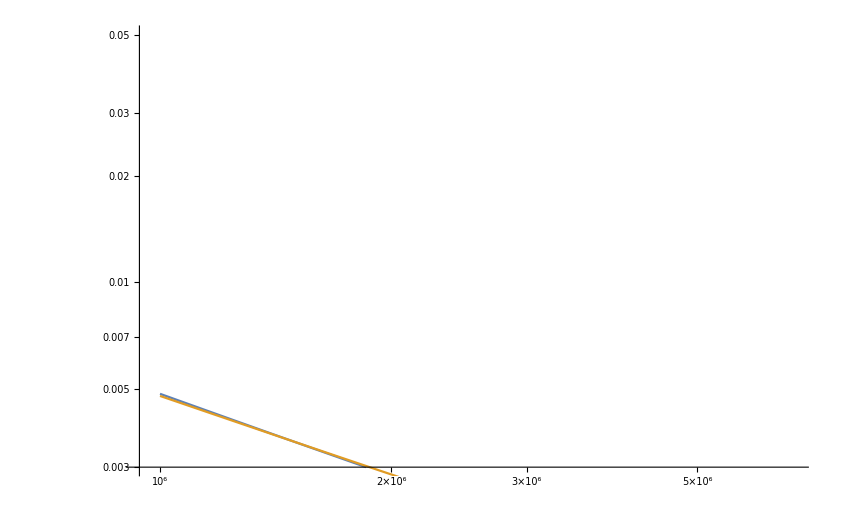

```mathematica
Show[{
LogLogPlot[FPSolutions[[1]],{Mass,10^6,10^6.8},PlotRange->{0.0030,0.05}],
LogLogPlot[FPSolutions[[2]]/.chi->-0.2,{Mass,10^6,10^6.8},PlotStyle->ColorData[97,2]]
}]
```

```mathematica
NSolve[FPSolutions/.chi->0,Mass]
```

NSolve[{(5.73893×10^-14 Re[1/Mass^0.206]^2 (5.72698×10^-7 Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-2.29079×10^-6 Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]))/((1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-4.3525×10^-11 Re[Mass^(3/4)] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]) (1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]+5.24772×10^-12 Re[1/Log[1.-0.0202 Mass^0.19]] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]))-(3.88048×10^-13 Re[1/Mass^0.206] (5.72698×10^-7 Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-2.29079×10^-6 Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]) Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]])/((1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-4.3525×10^-11 Re[Mass^(3/4)] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]) (1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]+5.24772×10^-12 Re[1/Log[1.-0.0202 Mass^0.19]] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]])),(5.73893×10^-14 Re[1/Mass^0.206]^2 (5.72698×10^-7 Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-2.29079×10^-6 Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]))/((1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-4.3525×10^-11 Re[Mass^(3/4)] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]) (1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]+5.24772×10^-12 Re[1/(0.+Log[1.-0.0202 Mass^0.19])] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]))-(3.88048×10^-13 Re[1/Mass^0.206] (5.72698×10^-7 Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-2.29079×10^-6 Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]) Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]])/((1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]-4.3525×10^-11 Re[Mass^(3/4)] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]) (1.94024×10^-13 Re[1/Mass^0.206] Re[1/(Log[1.-1.28947 Mass^(1/4)]-1. Log[1.-1.28947 ((1.-0.0202 Mass^0.19) Mass)^(1/4)])]+5.24772×10^-12 Re[1/(0.+Log[1.-0.0202 Mass^0.19])] Re[1/Log[1.-(1. (0.324 Mass^1.01+0.0202 Mass^1.19))/Mass]]))},Mass]

```mathematica
1/Log[Exp[-0.75]]
```

-1.33333

```mathematica
10^6.5
```

3.16228×10^6

```mathematica
1/Log[10^(-0.75),10]
```

-0.75

```mathematica
N[-4/3]
```

-1.33333

```mathematica
Log[%,10]
```

0.316879-1.48891 ⅈ

```mathematica
MassValues
```

{1.,1.77828,3.16228,5.62341,10.,17.7828,31.6228,56.2341,100.,177.828,316.228,562.341,1000.,1778.28,3162.28,5623.41,10000.,17782.8,31622.8,56234.1,100000.,177828.,316228.,562341.,1.×10^6,1.77828×10^6,3.16228×10^6,5.62341×10^6,1.×10^7,1.77828×10^7,3.16228×10^7,5.62341×10^7,1.×10^8,1.77828×10^8,3.16228×10^8,5.62341×10^8,1.×10^9}

```mathematica
ToString[ScientificForm[N[MassValues[[20]]],1]]
```

4
6. × 10

```mathematica
labels = Table[("10")^i,{i,0,9,0.25}]
```

{1.,10^0.25,10^0.5,10^0.75,10^1.,10^1.25,10^1.5,10^1.75,10^2.,10^2.25,10^2.5,10^2.75,10^3.,10^3.25,10^3.5,10^3.75,10^4.,10^4.25,10^4.5,10^4.75,10^5.,10^5.25,10^5.5,10^5.75,10^6.,10^6.25,10^6.5,10^6.75,10^7.,10^7.25,10^7.5,10^7.75,10^8.,10^8.25,10^8.5,10^8.75,10^9.}

```mathematica
labels[[5]]
```

1
1. × 10

```mathematica
S
```

1.×10^7

```mathematica
InvasionMass
```

{{10,{}},{100000,{}},{1000000,{}},{10000000,{}}}

```mathematica
SpSol
```

{{F→281.267,H→5.49913,FI→0,HI→0,R→0.980715},{F→0,H→0,FI→(1.70473×10^-13 (4.17596×10^-6+5.72698×10^-7 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])]))/((1.41094×10^-10 Re[(1+chi)^(3/4)]+4.6758×10^-14 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])]) (-9.56625×10^-12 Re[1/(-0.0780157+Log[1/(1.+chi)])]+4.6758×10^-14 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])])),HI→(3.33297×10^-15 (4.17596×10^-6+5.72698×10^-7 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])]))/((1.41094×10^-10 Re[(1+chi)^(3/4)]+4.6758×10^-14 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])]) (-9.56625×10^-12 Re[1/(-0.0780157+Log[1/(1.+chi)])]+4.6758×10^-14 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])])),R→(4.17596×10^-6 (-8.16452×10^-8-2.29079×10^-6 Re[1/(-0.0780157+Log[1/(1.+chi)])]))/(-9.56625×10^-12 Re[1/(-0.0780157+Log[1/(1.+chi)])]+4.6758×10^-14 Re[1/((-1.81012-3.14159 ⅈ)+Log[1.-7.25124 (1.+chi)^(1/4)])])}}

Stability of the Fixed Points

```mathematica
SolInternal = Solutions[[3;;4]]
```

{{F→(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),H→(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ)),FI→0,HI→0,R→(μ (-λ+σ))/(λ ρ+μ σ)},{F→0,H→0,FI→(α λ μ (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),HI→(α λ^2 (μ+ρ2))/((β2 μ+λ ρ2) (λ ρ2+μ σ2)),R→(μ (-λ+σ2))/(λ ρ2+μ σ2)}}

```mathematica
JacSpec = {
{D[FEq,F],D[FEq,H],D[FEq,FI],D[FEq,HI],D[FEq,R]},
{D[HEq,F],D[HEq,H],D[HEq,FI],D[HEq,HI],D[HEq,R]},
{D[FIEq,F],D[FIEq,H],D[FIEq,FI],D[FIEq,HI],D[FIEq,R]},
{D[HIEq,F],D[HIEq,H],D[HIEq,FI],D[HIEq,HI],D[HIEq,R]},
{D[REq,F],D[REq,H],D[REq,FI],D[REq,HI],D[REq,R]}
}
```

{{λ-(1-R) σ,R ρ,0,0,H ρ+F σ},{(1-R) σ,-μ-R ρ,0,0,-H ρ-F σ},{0,0,λ-(1-R) σ2,R ρ2,HI ρ2+FI σ2},{0,0,(1-R) σ2,-μ-R ρ2,-HI ρ2-FI σ2},{-R β,-R ρ,-R β2,-R ρ2,(1-R) α-R α-F β-FI β2-H ρ-HI ρ2}}

```mathematica
JacSpecSol1 = JacSpec/.SolInternal[[1]];
JacSpecSol2 =  JacSpec/.SolInternal[[2]];
```

```mathematica
Manipulate[
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^7,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.00001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324,
(*χ*)chi};
RF =Ratesfunc[parameters];
Growth=RF[[1]];
Starvation=RF[[2]];
Mortality=RF[[3]];
Recovery=RF[[4]];
Maintenance=RF[[5]];
Resourcegrowth=RF[[6]];
InvaderStarvation = RF[[7]];
InvaderRecovery=RF[[8]];
InvaderMaintenance=RF[[9]];

Eig1 = Eigenvalues[JacSpecSol1/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderMaintenance}];
Eig2 = Eigenvalues[JacSpecSol2/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality,σ2->InvaderStarvation,ρ2->InvaderRecovery,β2->InvaderMaintenance}];
REig1 = Re[Eig1];REig2= Re[Eig2];
IEig1 = Im[Eig1];IEig2 = Im[Eig2];
(*Row[{*)
Show[{
ListPlot[Transpose[{REig1,IEig1}],PlotRange->{{-1,1},{-1,1}},PlotStyle->ColorData[97,1]],
ListPlot[Transpose[{REig2,IEig2}],PlotRange->{{-1,1},{-1,1}},PlotStyle->ColorData[97,2]],
Graphics[{LightGray,Opacity[0.3],Disk[]}]
},ImageSize->300,Frame->True,AspectRatio->1,FrameLabel->{"Real part","Imaginary part"}],
(*FP=({R,H,F}/.Sol)/.{α->0.5,λ->0.1,μ->0.2,ρ->0.2,m->0.2,σ->sigma};
Show[{
ListPointPlot3D[FP,
PlotStyle->Directive[{ColorData[97,4],PointSize[Large]}],PlotLabel->FP,PlotRange->{{-1,1},{0,1},{0,1}},ImageSize->300,AxesLabel->{"R^*","S^*","F^*"}],
Graphics3D[{Opacity[0.5],Polygon[{{0,0,0},{0,1,0},{0,1,1},{0,0,1}}]}]
}]
}],*)
{{chi,0},-1,1,0.001}]
```

Part::partw: Part 2 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

Part::partw: Part 3 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

Part::partw: Part 4 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol2]], Im[Eigenvalues[JacSpecSol2]]} cannot be transposed.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}], PlotRange → {{-1, 1}, {-1, 1}}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.368417`, 0.506779`, 0.709798`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.24561133333333335`, 0.3378526666666667`, 0.4731986666666667`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Part::partw: Part 2 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

Part::partw: Part 3 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

Part::partw: Part 4 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol2]], Im[Eigenvalues[JacSpecSol2]]} cannot be transposed.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}], PlotRange → {{-1, 1}, {-1, 1}}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.368417`, 0.506779`, 0.709798`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.24561133333333335`, 0.3378526666666667`, 0.4731986666666667`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol2]], Im[Eigenvalues[JacSpecSol2]]} cannot be transposed.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}], PlotRange → {{-1, 1}, {-1, 1}}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.368417`, 0.506779`, 0.709798`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.24561133333333335`, 0.3378526666666667`, 0.4731986666666667`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol2]], Im[Eigenvalues[JacSpecSol2]]} cannot be transposed.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}], PlotRange → {{-1, 1}, {-1, 1}}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.368417`, 0.506779`, 0.709798`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.24561133333333335`, 0.3378526666666667`, 0.4731986666666667`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Part::partw: Part 2 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

Part::partw: Part 3 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

Part::partw: Part 4 of Ratesfunc[{0, 1, 10000000, 0.019, 0.0245, 10695., 3/4, -0.206, 3.3879×10^-7, 0.00001, 1.19, 1.01, 0.0202, 0.324, 0.357}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol2]], Im[Eigenvalues[JacSpecSol2]]} cannot be transposed.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}], PlotRange → {{-1, 1}, {-1, 1}}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.368417`, 0.506779`, 0.709798`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.24561133333333335`, 0.3378526666666667`, 0.4731986666666667`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]} cannot be transposed.

ListPlot::lpn: Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {Re[Eigenvalues[JacSpecSol2]], Im[Eigenvalues[JacSpecSol2]]} cannot be transposed.

Show::gcomb: Could not combine the graphics objects in {ListPlot[Transpose[{Re[Eigenvalues[JacSpecSol1]], Im[Eigenvalues[JacSpecSol1]]}], PlotRange → {{-1, 1}, {-1, 1}}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[RGBColor[0.368417`, 0.506779`, 0.709798`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, RGBColor[0.24561133333333335`, 0.3378526666666667`, 0.4731986666666667`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

```mathematica
REig1
REig2
```

{-0.494133,-5.38414×10^-6,-5.34837×10^-6,-1.21891×10^-8,1.3204×10^-23}

{-0.494133,-5.38414×10^-6,-5.34837×10^-6,-1.21891×10^-8,9.71744×10^-19}